### Full Generality

```mathematica
α = ({{α1}, {α2}, {α3}});
c0=({{c01}, {A021}, {c03}}); (* A021 == c02 to satisfy the 0.5 constraint *)
c1=({{c11}, {c12}, {c13}});
β1=({{β11}, {β12}, {β13}});
β2=({{β21}, {β22}, {β23}});
A0=({{0, 0, 0}, {A021, 0, 0}, {A031, A032, 0}}); (* A0=({{A011, A012, A013}, {A021, A022, A023}, {A031, A032, A033}}); *)
B0=({{0, 0, 0}, {B021, 0, 0}, {B031, B032, 0}}); (* Subscript[B, 0]=({{B011, B012, B013}, {B021, B022, B023}, {B031, B032, B033}}); *)
H0=({{H01}, {H02}, {H03}});
VU=({{U}, {U}, {U}});
e = ({{1}, {1}, {1}});
```

```mathematica
K1=IdentityMatrix[3] - μ h A0 ;
MatrixForm[K1 ]
```

(1 | 0 | 0
-A021 h μ | 1 | 0
-A031 h μ | -A032 h μ | 1)

```mathematica
K2 = VU + B0 . e  σ (σ I10)/h;
MatrixForm[K2]
```

(U
U+1/2 B021 (W+Z/(√3)) σ^2
U+1/2 (B031+B032) (W+Z/(√3)) σ^2)

```mathematica
H0= Inverse[K1].K2;
MatrixForm[H0]
```

(U
U+A021 h U μ+1/2 B021 (W+Z/(√3)) σ^2
U+U (A031 h μ+A021 A032 h^2 μ^2)+1/2 (B031+B032) (W+Z/(√3)) σ^2+A032 h μ (U+1/2 B021 (W+Z/(√3)) σ^2))

```mathematica
U2= U+ μ h αᵀ.H0 + σ I1 Transpose[e].β1+ σ I10/h Transpose[e].β2;
U2 =U2[[1]][[1]];
U2
```

U+W (β11+β12+β13) σ+1/2 (W+Z/(√3)) (β21+β22+β23) σ+h μ (U α1+α2 (U+A021 h U μ+1/2 B021 (W+Z/(√3)) σ^2)+α3 (U+U (A031 h μ+A021 A032 h^2 μ^2)+1/2 (B031+B032) (W+Z/(√3)) σ^2+A032 h μ (U+1/2 B021 (W+Z/(√3)) σ^2)))

```mathematica
I10=1/2 h(W+Z/(√3)); 
I1= W;
```

```mathematica
U2Full = U2
```

U+W (β11+β12+β13) σ+1/2 (W+Z/(√3)) (β21+β22+β23) σ+h μ (U α1+α2 (U+A021 h U μ+1/2 B021 (W+Z/(√3)) σ^2)+α3 (U+U (A031 h μ+A021 A032 h^2 μ^2)+1/2 (B031+B032) (W+Z/(√3)) σ^2+A032 h μ (U+1/2 B021 (W+Z/(√3)) σ^2)))

```mathematica
U2Plugged = U2Full /.  {W -> 0,Z->0}
G = Coefficient[U2Plugged,U]
```

U+h μ (U α1+α2 (U+A021 h U μ)+α3 (U+A032 h U μ+U (A031 h μ+A021 A032 h^2 μ^2)))

1+h α1 μ+h α2 μ+h α3 μ+A021 h^2 α2 μ^2+A031 h^2 α3 μ^2+A032 h^2 α3 μ^2+A021 A032 h^3 α3 μ^3

```mathematica
stableeq = G/.  {μ -> z/h}
```

1+z α1+z α2+A021 z^2 α2+z α3+A031 z^2 α3+A032 z^2 α3+A021 A032 z^3 α3

```mathematica
1+z Transpose[α].Inverse[K1].e /.  {μ -> z/h}
```

{{1+z (α1+α2+A021 z α2+α3+A032 z α3+(A031 z+A021 A032 z^2) α3)}}

```mathematica
FullSimplify[1+z (α1+α2+A021 z α2+α3+A032 z α3+(A031 z+A021 A032 z^2) α3)]
```

1+z (α1+α2+A021 z α2+α3+z (A031+A032+A021 A032 z) α3)

```mathematica
Solve[{1+z (α1+α2+A021 z α2+α3+z (A031+A032+A021 A032 z) α3) == 1},z]
```

{{z→0},{z→(-A021 α2-A031 α3-A032 α3-√(-4 A021 A032 α3 (α1+α2+α3)+(A021 α2+A031 α3+A032 α3)^2))/(2 A021 A032 α3)},{z→(-A021 α2-A031 α3-A032 α3+√(-4 A021 A032 α3 (α1+α2+α3)+(A021 α2+A031 α3+A032 α3)^2))/(2 A021 A032 α3)}}

```mathematica
Solve[{1+z (α1+α2+A021 z α2+α3+z (A031+A032+A021 A032 z) α3)== -1},z]
```

{{z→-(A021 α2+A031 α3+A032 α3)/(3 A021 A032 α3)-(2^(1/3) (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2))/(3 A021 A032 α3 (-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3+√((-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3)^2+4 (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2)^3))^(1/3))+1/(3 2^(1/3) A021 A032 α3)(-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3+√((-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3)^2+4 (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2)^3))^(1/3)},{z→-(A021 α2+A031 α3+A032 α3)/(3 A021 A032 α3)+((1+ⅈ √3) (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2))/(3 2^(2/3) A021 A032 α3 (-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3+√((-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3)^2+4 (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2)^3))^(1/3))-1/(6 2^(1/3) A021 A032 α3)(1-ⅈ √3) (-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3+√((-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3)^2+4 (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2)^3))^(1/3)},{z→-(A021 α2+A031 α3+A032 α3)/(3 A021 A032 α3)+((1-ⅈ √3) (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2))/(3 2^(2/3) A021 A032 α3 (-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3+√((-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3)^2+4 (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2)^3))^(1/3))-1/(6 2^(1/3) A021 A032 α3)(1+ⅈ √3) (-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3+√((-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3)^2+4 (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2)^3))^(1/3)}}

```mathematica
cond1 = First[First[Transpose[α].e]] == 1;
cond2 = First[First[Transpose[β1].e]] == 1;
cond3 = First[First[Transpose[β2].e]] == 0;
cond4 = First[First[Transpose[α].B0.e]] == 1;
cond5 = First[First[Transpose[α].A0.e]] == 1/2;
cond6 = First[First[Transpose[α].(B0.e)^2]] == 3/2;
cond7 = First[First[Transpose[β1].c1]] == 1;
cond8 = First[First[Transpose[β2].c1]] == -1;
vars = {α1,α2,α3,c01,c03,c11,c12,c13,β11,β12,β13,β21,β22,β23,A021,A031,A032,B021,B031,B032};
```

```mathematica
conds = {cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8}
FindInstance[conds ,vars,Reals]
```

{α1+α2+α3==1,β11+β12+β13==1,β21+β22+β23==0,B021 α2+B031 α3+B032 α3==1,A021 α2+A031 α3+A032 α3==1/2,B021^2 α2+(B031+B032)^2 α3==3/2,c11 β11+c12 β12+c13 β13==1,c11 β21+c12 β22+c13 β23==-1}

{{α1→1/3,α2→0,α3→2/3,c01→8/5,c03→2,c11→-1,c12→0,c13→0,β11→-1,β12→0,β13→2,β21→1,β22→0,β23→-1,A021→0,A031→0,A032→3/4,B021→0,B031→0,B032→3/2}}

```mathematica
Minimize[{Min[(-A021 α2-A031 α3-A032 α3-√(-4 A021 A032 α3 (α1+α2+α3)+(A021 α2+A031 α3+A032 α3)^2))/(2 A021 A032 α3),0],Min[(-A021 α2-A031 α3-A032 α3+√(-4 A021 A032 α3 (α1+α2+α3)+(A021 α2+A031 α3+A032 α3)^2))/(2 A021 A032 α3),0],
Min[-(A021 α2+A031 α3+A032 α3)/(3 A021 A032 α3)-(2^(1/3) (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2))/(3 A021 A032 α3 (-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3+√((-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3)^2+4 (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2)^3))^(1/3))+1/(3 2^(1/3) A021 A032 α3)(-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3+√((-2 A021^3 α2^3+9 A021^2 A032 α1 α2 α3-6 A021^2 A031 α2^2 α3+3 A021^2 A032 α2^2 α3-54 A021^2 A032^2 α3^2+9 A021 A031 A032 α1 α3^2+9 A021 A032^2 α1 α3^2-6 A021 A031^2 α2 α3^2+9 A021^2 A032 α2 α3^2-3 A021 A031 A032 α2 α3^2+3 A021 A032^2 α2 α3^2-2 A031^3 α3^3+9 A021 A031 A032 α3^3-6 A031^2 A032 α3^3+9 A021 A032^2 α3^3-6 A031 A032^2 α3^3-2 A032^3 α3^3)^2+4 (3 A021 A032 α3 (α1+α2+α3)-(A021 α2+A031 α3+A032 α3)^2)^3))^(1/3),0],cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8},vars,Reals]
```

$Aborted

```mathematica
Minimize[{Min[(-A021 α2-A031 α3-A032 α3-√(-4 A021 A032 α3 (α1+α2+α3)+(A021 α2+A031 α3+A032 α3)^2))/(2 A021 A032 α3),0],cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,A031+A032== c03},vars,Reals]
```

Minimize::natt: The minimum is not attained at any point satisfying the given constraints.

{-∞,{α1→Indeterminate,α2→Indeterminate,α3→Indeterminate,c01→Indeterminate,c03→Indeterminate,c11→Indeterminate,c12→Indeterminate,c13→Indeterminate,β11→Indeterminate,β12→Indeterminate,β13→Indeterminate,β21→Indeterminate,β22→Indeterminate,β23→Indeterminate,A021→Indeterminate,A031→Indeterminate,A032→Indeterminate,B021→Indeterminate,B031→Indeterminate,B032→Indeterminate}}

```mathematica
Minimize[{(-A021 α2-A031 α3-A032 α3+√(-4 A021 A032 α3 (α1+α2+α3)+(A021 α2+A031 α3+A032 α3)^2))/(2 A021 A032 α3),cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,A031+A032== c03,A021 > 0,c11>0},vars,Reals]
```

$Aborted

```mathematica
Minimize[{(-A021 α2-A031 α3-A032 α3+√(-4 A021 A032 α3 (α1+α2+α3)+(A021 α2+A031 α3+A032 α3)^2))/(2 A021 A032 α3),cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,A031+A032== c03,A021 == 1},vars,Reals]
```

{-4,{α1→13/4,α2→-7/2,α3→5/4,c01→0,c03→16/5,c11→-2,c12→-5,c13→0,β11→2,β12→-1,β13→0,β21→3,β22→-1,β23→-2,A021→1,A031→63/20,A032→1/20,B021→-1,B031→0,B032→-2}}

```mathematica
Minimize[{(-A021 α2-A031 α3-A032 α3+√(-4 A021 A032 α3 (α1+α2+α3)+(A021 α2+A031 α3+A032 α3)^2))/(2 A021 A032 α3),cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,A031+A032== c03,A021 > 0},vars,Reals]
```

{-4,{α1→13/4,α2→-7/2,α3→5/4,c01→0,c03→16/5,c11→-2,c12→-5,c13→0,β11→2,β12→-1,β13→0,β21→3,β22→-1,β23→-2,A021→1,A031→63/20,A032→1/20,B021→-1,B031→0,B032→-2}}

```mathematica
Minimize[{(-A021 α2-A031 α3-A032 α3+√(-4 A021 A032 α3 (α1+α2+α3)+(A021 α2+A031 α3+A032 α3)^2))/(2 A021 A032 α3),cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,A031+A032== c03,A021 == 1,c03<1},vars,Reals]
```

{-4,{α1→13/4,α2→5/4,α3→-7/2,c01→0,c03→3/14,c11→-2,c12→-5,c13→0,β11→2,β12→-1,β13→0,β21→3,β22→-1,β23→-2,A021→1,A031→13/56,A032→-1/56,B021→-2,B031→0,B032→-1}}

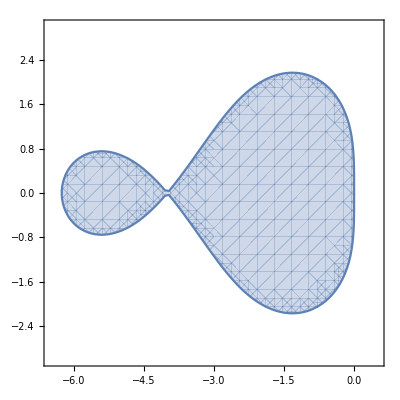

```mathematica
RegionPlot[Abs[1+z (α1+α2+A021 z α2+α3+A032 z α3+(A031 z+A021 A032 z^2) α3)/. {z-> x + ⅈ y,A021->1,A031->13/56,A032->-1/56,α1->13/4,α2->5/4,α3->-7/2}]<1,{x,-6.5,0.5},{y,-3,3}]
```

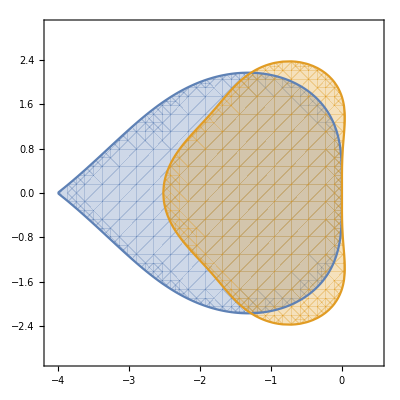

```mathematica
RegionPlot[{Abs[1+z (α1+α2+A021 z α2+α3+A032 z α3+(A031 z+A021 A032 z^2) α3)/. {z-> x + ⅈ y,A021->1,A031->63/20,A032->1/20,α1->13/4,α2->-7/2,α3->5/4}]<1,Abs[1+z (α1+α2+A021 z α2+α3+A032 z α3+(A031 z+A021 A032 z^2) α3)/. {z-> x + ⅈ y,A021-> 1,A031->1/4, A032-> 1/4,α1->1/6,α2->1/6,α3-> 2/3}]<1},{x,-4.1,0.5},{y,-3,3}]
```

```mathematica
NIntegrate[Boole[Abs[1+z (α1+α2+A021 z α2+α3+A032 z α3+(A031 z+A021 A032 z^2) α3)/. {z-> x + ⅈ y,A021->1,A031->13/56,A032->-1/56,α1->13/4,α2->5/4,α3->-7/2}]<1],{x,-4.1,0.5},{y,-3,3}]
```

12.1215

```mathematica
NMaximize[{Chi[α1,α2,α3,A021,A031,A032],cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8,A031+A032== c03,A021 == 1},vars,Reals]
```

$Aborted

```mathematica
Chi[A021_,A031_,A032_,α1_,α2_,α3_] :=N[(Total[Total[Boole[Table[Abs[1+z (α1+α2+A021 z α2+α3+A032 z α3+(A031 z+A021 A032 z^2) α3)/. {z-> x + ⅈ y}]<1,{x,-4,1,.02},{y,-3,3,.02}]]]]/75551)*(5*6)]
```

```mathematica
Chi[1,13/56,-1/56,13/4,5/4,-7/2]
```

12.0169

```mathematica
Chi[ 1,1/4, 1/4,1/6,1/6, 2/3]
```

9.08715

```mathematica
Total[Total[Table[1,{x,-4,1,.02},{y,-3,3,.02}]]]
```

75551

```mathematica
α = ({{a1}, {a2}, {a3}});
c0=({{c01}, {A021}, {c03}}); (* A021 == c02 to satisfy the 0.5 constraint *)
c1=({{c11}, {c12}, {c13}});
β1=({{b11}, {b12}, {b13}});
β2=({{b21}, {b22}, {b23}});
A0=({{0, 0, 0}, {A021, 0, 0}, {A031, A032, 0}}); (* A0=({{A011, A012, A013}, {A021, A022, A023}, {A031, A032, A033}}); *)
B0=({{0, 0, 0}, {B021, 0, 0}, {B031, B032, 0}}); (* Subscript[B, 0]=({{B011, B012, B013}, {B021, B022, B023}, {B031, B032, B033}}); *)
H0=({{H01}, {H02}, {H03}});
VU=({{U}, {U}, {U}});
e = ({{1}, {1}, {1}});
```

```mathematica
cond1 = First[First[Transpose[α].e]] == 1;
cond2 = First[First[Transpose[β1].e]] == 1;
cond3 = First[First[Transpose[β2].e]] == 0;
cond4 = First[First[Transpose[α].B0.e]] == 1;
cond5 = First[First[Transpose[α].A0.e]] == 1/2;
cond6 = First[First[Transpose[α].(B0.e)^2]] == 3/2;
cond7 = First[First[Transpose[β1].c1]] == 1;
cond8 = First[First[Transpose[β2].c1]] == -1;
vars = {a1,a2,a3,c01,c03,c11,c12,c13,b11,b12,b13,b21,b22,b23,A021,A031,A032,B021,B031,B032};
```

```mathematica
conds = {cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8}
```

{a1+a2+a3==1,b11+b12+b13==1,b21+b22+b23==0,a2 B021+a3 B031+a3 B032==1,A021 a2+A031 a3+A032 a3==1/2,a2 B021^2+a3 (B031+B032)^2==3/2,b11 c11+b12 c12+b13 c13==1,b21 c11+b22 c12+b23 c13==-1}

```mathematica
c02=A021;
a1=1-a2-a3;
b11=1-b12-b13;
b21=-b22-b23;
c03=A031+A032;
c12 = (-1-b21 c11-b23 c13)/b22;
b12 = (b22 (1-c11+b13 c11-b13 c13))/(-1+b23 c11-b23 c13);
```

```mathematica
conds = FullSimplify[{cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8}]
```

{True,True,True,(B021 (2 A031 (-1+a2 B021)+B031+B032-2 (A032-A032 a2 B021+A021 a2 (B031+B032))))/((A031+A032) B021-A021 (B031+B032))==0,2 A021 a2+((A031+A032) (-2 A021+B021))/((A031+A032) B021-A021 (B031+B032))==1,a2 B021^2+((-2 A021+B021) (B031+B032)^2)/(2 ((A031+A032) B021-A021 (B031+B032)))==3/2,True,True}

```mathematica
Solve[2 A021 a2+((A031+A032) (-2 A021+B021))/((A031+A032) B021-A021 (B031+B032))==1,a2]
```

{{a2→(2 A031+2 A032-B031-B032)/(2 (A031 B021+A032 B021-A021 B031-A021 B032))}}